```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma[a_]=gamma0+gammap0(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma[a];
```

```mathematica
om=0.3;
gamma0=0.55;
gammap0=-0.01;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

Set::write: Tag Integer in (-1)[z_] is Protected.

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
q[0]
```

-12.3896

-0.04

Set::write: Tag Integer in (-1)[z_] is Protected.

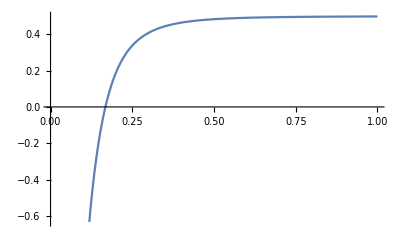

-12.3896

```mathematica
gammap0=-0.04
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p04=Plot[q[z],{z,0,1}]
q[0]
```

```mathematica
gammap0=-0.03
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p5=Plot[q[z],{z,0,1}]
q[0]
```

-0.03

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=-0.02
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p02=Plot[q[z],{z,0,1}]
q[0]
```

-0.02

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=-0.01
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p1=Plot[q[z],{z,0,1}]
q[0]
```

-0.01

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p0=Plot[q[z],{z,0,1}]
q[0]
```

0

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0.01
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

0.01

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=0.02
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p22=Plot[q[z],{z,0,1}]
q[0]
```

0.02

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0.03
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

0.03

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=0.04
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p44=Plot[q[z],{z,0,1}]
q[0]
```

0.04

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0list={-0.04,-0.03,-0.02,-0.01,0,0.01,0.02,0.03,0.04}
```

{-0.04,-0.03,-0.02,-0.01,0,0.01,0.02,0.03,0.04}

```mathematica
q0={-0.45003261289085594, -0.570429893323448, -0.6908271737560423, -0.8112244541886344, -0.9316217346212232, -1.0520190150538227, -1.172416295486416, -1.2928135759190102, -1.4132108563516035}
```

{-0.450033,-0.57043,-0.690827,-0.811224,-0.931622,-1.05202,-1.17242,-1.29281,-1.41321}

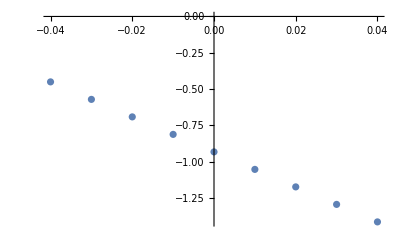

```mathematica
data1=Transpose@{gammap0list,q0};
list1=ListPlot[data1]
```

```mathematica
om=0.3;
gamma0=0.59;
gammap0=-0.01;
```

```mathematica
gammap0=-0.04
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

-0.04

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=-0.03
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

-0.03

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=-0.02
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p2=Plot[q[z],{z,0,1}]
q[0]
```

-0.02

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=-0.01
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

-0.01

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=0
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
Plot[q[z],{z,0,1}]
q[0]
```

0

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0.01
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

0.01

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

0.02

Set::write: Tag Integer in (-1)[z_] is Protected.

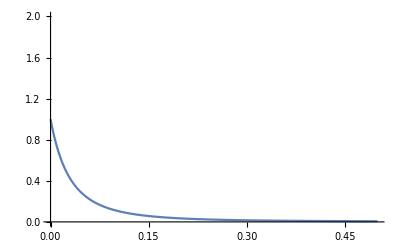

-12.3896

```mathematica
gammap0=0.02
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
Plot[Fz[z],{z,0,0.5},PlotRange->{0,2}]
q[0]
```

```mathematica
gammap0=0.03
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

0.03

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=0.04
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];

Plot[q[z],{z,0,1}]
q[0]
```

0.04

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
q0={0.34608183156240147, 0.27919445354429406, 0.21230707552618555, 0.14541969750807815, 0.07853231948997141, 0.011644941471863568, -0.055242436546243834, -0.1221298145643519, -0.1890171925824592}
```

{0.346082,0.279194,0.212307,0.14542,0.0785323,0.0116449,-0.0552424,-0.12213,-0.189017}

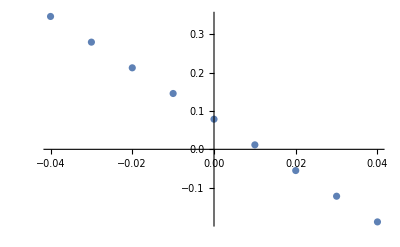

```mathematica
data3=Transpose@{gammap0list,q0};
list3=ListPlot[data3]
```

```mathematica
om=0.3;
gamma0=0.51;
gammap0=-0.01;
```

```mathematica
gammap0=-0.04
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
Plot[q[z],{z,0,1}]
q[0]
```

-0.04

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=-0.03
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

-0.03

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=-0.02
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

-0.02

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=-0.01
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
p3=Plot[q[z],{z,0,1}]
q[0]
```

-0.01

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
Plot[q[z],{z,0,1}]
q[0]
```

0

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0.01
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

0.01

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=0.02
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
Plot[Fz[z],{z,0,0.5},PlotRange->{0,2}]
q[0]
```

0.02

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
gammap0=0.03
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
q[0]
```

0.03

Set::write: Tag Integer in (-1)[z_] is Protected.

-12.3896

```mathematica
gammap0=0.04
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
Fa[a_]= efe[a]/.Flatten[sol];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
Fz[z_]=Fa[1/(1+z)];
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
q[z_]:= -1 + (1+z)ez'[z]/ez[z];

Plot[q[z],{z,0,1}]
q[0]
```

0.04

Set::write: Tag Integer in (-1)[z_] is Protected.

-Graphics-

-12.3896

```mathematica
q0={-3.1231267624131585, -3.424119963494644, -3.7251131645761246, -4.0261063656576095, -4.3270995667390855, -4.6280927678205845, -4.92908596890207, -5.230079169983556, -5.531072371065036}
```

{-3.12313,-3.42412,-3.72511,-4.02611,-4.3271,-4.62809,-4.92909,-5.23008,-5.53107}

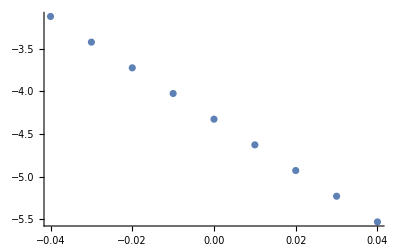

```mathematica
data2=Transpose@{gammap0list,q0};
list2=ListPlot[data2]
```

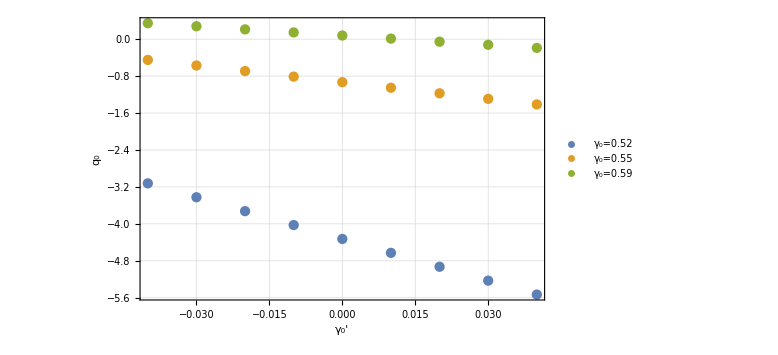

```mathematica
list=ListPlot[{data2,data1,data3}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_0'", Black, FontSize->24],Style["q_0", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0=0.52", "γ_0=0.55", "γ_0=0.59"},LegendFunction->"Frame", Background->White],{Left,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}]
```

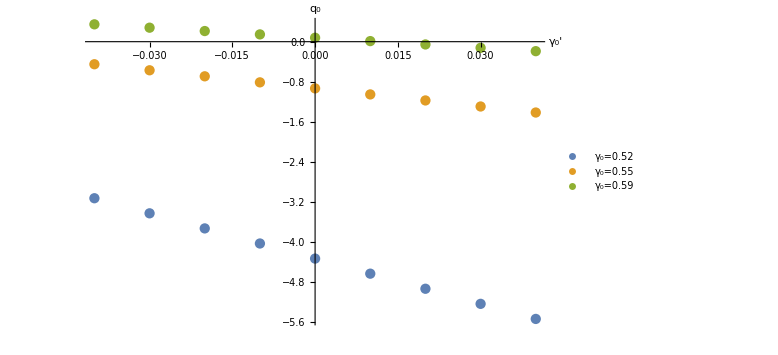

```mathematica
test=ListPlot[{data2,data1,data3}, PlotLegends->{"γ_0=0.52", "γ_0=0.55", "γ_0=0.59"},AxesLabel->{Style["γ_0'", Black, FontSize->20],Style["q_0", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->Thick, ImageSize->Large]
```

```mathematica
data2
```

{{-0.04,-3.12313},{-0.03,-3.42412},{-0.02,-3.72511},{-0.01,-4.02611},{0,-4.3271},{0.01,-4.62809},{0.02,-4.92909},{0.03,-5.23008},{0.04,-5.53107}}

```mathematica
Fit[data2, {1,z},z]
Fit[data1, {1,z},z]
Fit[data3, {1,z},z]
```

-4.3271-30.0993 z

-0.931622-12.0397 z

0.0785323-6.68874 z

```mathematica
fit2=Plot[-4.327099566739099-30.0993201081485*z,{z,-0.04,0.04}, PlotStyle->Blue];
```

```mathematica
fit1=Plot[-0.9316217346212287-12.039728043259355*z,{z,-0.04,0.04}, PlotStyle->Orange];
```

```mathematica
fit3=Plot[0.07853231948997105-6.688737801810758*z,{z,-0.04,0.04}, PlotStyle->Green];
plot=Plot[-0.5+0.08,{z,-0.04,0.04}, PlotStyle->{Black, Dashed, Thick}];
plot2=Plot[-0.5-0.08,{z,-0.04,0.04}, PlotStyle->{Black, Dashed, Thick}];
```

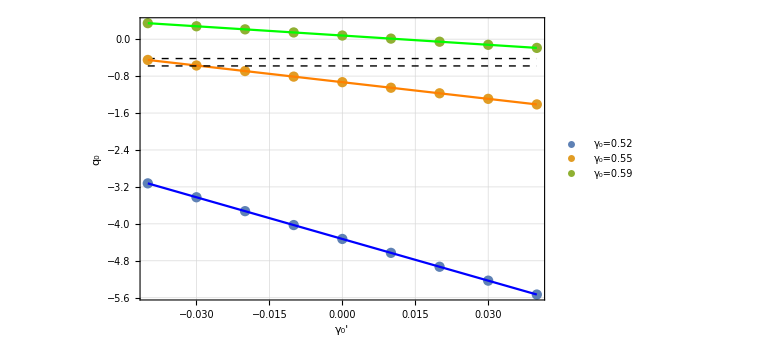

```mathematica
graficoq0gamma=Show[{list,fit1,fit2,fit3,plot,plot2}]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\final_plots"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\final_plots

```mathematica
Export["q0_gamma0'(z).png",graficoq0gamma,ImageResolution->700]
```

q0_gamma0'(z).png